```mathematica
L1=({{((m+k)^2-m^2)/(2 Subscript[R, 0]^2)+Subscript[u, a] Φ^2-ω, Subscript[u, a] Φ^2, (g+ⅈ/2 Subscript[R, 1])Φ}, {-Subscript[u, a] Φ^2, -(((m-k)^2-m^2)/(2 Subscript[R, 0]^2)+Subscript[u, a] Φ^2)-ω, -(g-ⅈ/2 Subscript[R, 1])Φ}, {-ⅈ Subscript[R, 1] Φ Subscript[n, 0], -ⅈ Subscript[R, 1] Φ Subscript[n, 0], -ⅈ(Subscript[γ, R]+Subscript[R, 1] Φ^2)-ω}});
F=Det[L1];
FP=F/.{g->2 Subscript[u, a],Φ->√(1/Subscript[R, 1](P/Subscript[n, 0]-Subscript[γ, R]))}/.{Subscript[n, 0]->Subscript[γ, c]/Subscript[R, 1],P->P1 Pth}/.{Pth->(Subscript[γ, R] Subscript[γ, c])/Subscript[R, 1]};
```

```mathematica
ComplexExpand[F]
```

-ω^3+(k^4 ω)/(4 R_0^4)-(k^2 m^2 ω)/R_0^4+(2 k m ω^2)/R_0^2+Φ^2 ω n_0 R_1^2-(k m Φ^2 n_0 R_1^2)/R_0^2+(k^2 Φ^2 ω u_a)/R_0^2+ⅈ (-Φ^2 ω^2 R_1+(k^4 Φ^2 R_1)/(4 R_0^4)-(k^2 m^2 Φ^2 R_1)/R_0^4+(2 k m Φ^2 ω R_1)/R_0^2-(g k^2 Φ^2 n_0 R_1)/R_0^2+(k^2 Φ^4 R_1 u_a)/R_0^2-ω^2 γ_R+(k^4 γ_R)/(4 R_0^4)-(k^2 m^2 γ_R)/R_0^4+(2 k m ω γ_R)/R_0^2+(k^2 Φ^2 u_a γ_R)/R_0^2)

```mathematica
re=Solve[-ω^3+(k^4 ω)/(4 Subscript[R, 0]^4)-(k^2 m^2 ω)/Subscript[R, 0]^4+(2 k m ω^2)/Subscript[R, 0]^2+Φ^2 ω Subscript[n, 0] Subscript[R, 1]^2-(k m Φ^2 Subscript[n, 0] Subscript[R, 1]^2)/Subscript[R, 0]^2==0,ω];
```

```mathematica
o1=First[First[re]];
```

```mathematica
ImF=(-Φ^2 ω^2 Subscript[R, 1]+(k^4 Φ^2 Subscript[R, 1])/(4 Subscript[R, 0]^4)-(k^2 m^2 Φ^2 Subscript[R, 1])/Subscript[R, 0]^4+(2 k m Φ^2 ω Subscript[R, 1])/Subscript[R, 0]^2-(g k^2 Φ^2 Subscript[n, 0] Subscript[R, 1])/Subscript[R, 0]^2+(k^2 Φ^4 Subscript[R, 1] Subscript[u, a])/Subscript[R, 0]^2-ω^2 Subscript[γ, R]+(k^4 Subscript[γ, R])/(4 Subscript[R, 0]^4)-(k^2 m^2 Subscript[γ, R])/Subscript[R, 0]^4+(2 k m ω Subscript[γ, R])/Subscript[R, 0]^2+(k^2 Φ^2 Subscript[u, a] Subscript[γ, R])/Subscript[R, 0]^2);
```

```mathematica
kstar=ImF/.o1/.{g->2 Subscript[u, a],Φ->√(1/Subscript[R, 1](P/Subscript[n, 0]-Subscript[γ, R]))}/.{Subscript[n, 0]->Subscript[γ, c]/Subscript[R, 1],P->P1 Pth}/.{Pth->(Subscript[γ, R] Subscript[γ, c])/Subscript[R, 1]};
```

```mathematica
Collect[eqImF,k];
```

```mathematica
Par={Subscript[u, a]->7.7*10^-3,Subscript[γ, R]->1.5,Subscript[γ, c]->1,Subscript[R, 1]->8.4*10^-3,P1->2.5,Subscript[R, 0]->16*√5/√2};

re2=Solve[-Φ^2 ω^2 Subscript[R, 1]+(k^4 Φ^2 Subscript[R, 1])/(4 Subscript[R, 0]^4)-(k^2 m^2 Φ^2 Subscript[R, 1])/Subscript[R, 0]^4+(2 k m Φ^2 ω Subscript[R, 1])/Subscript[R, 0]^2-(g k^2 Φ^2 Subscript[n, 0] Subscript[R, 1])/Subscript[R, 0]^2+(k^2 Φ^4 Subscript[R, 1] Subscript[u, a])/Subscript[R, 0]^2-ω^2 Subscript[γ, R]+(k^4 Subscript[γ, R])/(4 Subscript[R, 0]^4)-(k^2 m^2 Subscript[γ, R])/Subscript[R, 0]^4+(2 k m ω Subscript[γ, R])/Subscript[R, 0]^2+(k^2 Φ^2 Subscript[u, a] Subscript[γ, R])/Subscript[R, 0]^2==0,ω];
re2o1=First[First[re2]];
re2o2=Last[Last[re2]];
kstar2a=-ω^3+(k^4 ω)/(4 Subscript[R, 0]^4)-(k^2 m^2 ω)/Subscript[R, 0]^4+(2 k m ω^2)/Subscript[R, 0]^2+Φ^2 ω Subscript[n, 0] Subscript[R, 1]^2-(k m Φ^2 Subscript[n, 0] Subscript[R, 1]^2)/Subscript[R, 0]^2+(k^2 Φ^2 ω Subscript[u, a])/Subscript[R, 0]^2/.re2o1/.{g->2 Subscript[u, a],Φ->√(1/Subscript[R, 1](P/Subscript[n, 0]-Subscript[γ, R]))}/.{Subscript[n, 0]->Subscript[γ, c]/Subscript[R, 1],P->P1 Pth}/.{Pth->(Subscript[γ, R] Subscript[γ, c])/Subscript[R, 1]};
kstar2b=-ω^3+(k^4 ω)/(4 Subscript[R, 0]^4)-(k^2 m^2 ω)/Subscript[R, 0]^4+(2 k m ω^2)/Subscript[R, 0]^2+Φ^2 ω Subscript[n, 0] Subscript[R, 1]^2-(k m Φ^2 Subscript[n, 0] Subscript[R, 1]^2)/Subscript[R, 0]^2+(k^2 Φ^2 ω Subscript[u, a])/Subscript[R, 0]^2/.re2o2/.{g->2 Subscript[u, a],Φ->√(1/Subscript[R, 1](P/Subscript[n, 0]-Subscript[γ, R]))}/.{Subscript[n, 0]->Subscript[γ, c]/Subscript[R, 1],P->P1 Pth}/.{Pth->(Subscript[γ, R] Subscript[γ, c])/Subscript[R, 1]};
```

```mathematica
(*kstar2a is the correct equation*)

Largem=Series[kstar2a,{m,∞,1}]
```

(2 (-k^3 u_a γ_c+k^3 P1 u_a γ_c) m)/(P1 R_0^4 R_1)-1/(2 (P1^2 R_0^6 R_1 γ_R))√((k^2 P1 R_0^4 γ_R^2 (k^2 P1 R_1+8 R_0^2 u_a γ_c-8 P1 R_0^2 u_a γ_c-4 P1 R_0^2 u_a γ_R+4 P1^2 R_0^2 u_a γ_R))/R_1) (-2 k^2 u_a γ_c+2 k^2 P1 u_a γ_c-P1 R_0^2 R_1 γ_c γ_R+P1^2 R_0^2 R_1 γ_c γ_R)+O[1/m]^2

```mathematica
LargeM=Normal[Largem]
```

(2 m (-k^3 u_a γ_c+k^3 P1 u_a γ_c))/(P1 R_0^4 R_1)-1/(2 P1^2 R_0^6 R_1 γ_R)√((k^2 P1 R_0^4 γ_R^2 (k^2 P1 R_1+8 R_0^2 u_a γ_c-8 P1 R_0^2 u_a γ_c-4 P1 R_0^2 u_a γ_R+4 P1^2 R_0^2 u_a γ_R))/R_1) (-2 k^2 u_a γ_c+2 k^2 P1 u_a γ_c-P1 R_0^2 R_1 γ_c γ_R+P1^2 R_0^2 R_1 γ_c γ_R)

```mathematica
kv=ToRadicals[NSolve[{LargeM/.Par}==0,k]];
```

```mathematica
kv4=First[Take[kv,{4,4}]];
kv5=First[Take[kv,{5,5}]];
```

```mathematica
(*Plot[k/.kv3/.Par,{m,60,110}]*)
```

```mathematica
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]];
```

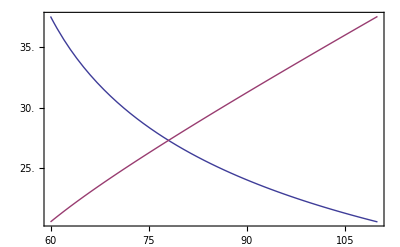

```mathematica
TwoAxisPlot[{k/.kv4/.Par,k/.kv5/.Par},{m,60,110}]
```

```mathematica
Length[kv]
```

7

```mathematica
Collect[LargeM/.Par/.m->70,k]
```

```mathematica
Subscript[u, a] Φ^2/.{g->2 Subscript[u, a],Φ->√(1/Subscript[R, 1](P/Subscript[n, 0]-Subscript[γ, R]))}/.{Subscript[n, 0]->Subscript[γ, c]/Subscript[R, 1],P->P1 Pth}/.{Pth->(Subscript[γ, R] Subscript[γ, c])/Subscript[R, 1]}
```

(u_a (-γ_R+P1 γ_R))/R_1

```mathematica
Out[80]/.Par
```

2.0625